```mathematica
Remove["Global`*"]
```

### Simulation of Pendulum motion

```mathematica
$Assumptions={m,g,l,tc,tp}∈Reals
```

(m|g|l|tc|tp)∈ℝ

Define the drive (input) function.

```mathematica
tdrive[t_,tc_,tp_]=tc (UnitStep[t]-UnitStep[t-tp])
```

tc (UnitStep[t]-UnitStep[t-tp])

Define the non-linear equation:

```mathematica
deqn= m l^2 θ''[t] + m g l Sin[θ[t]]== tdrive[t,tc,tp]
```

g l m Sin[θ[t]]+l^2 m θ''[t]==tc (UnitStep[t]-UnitStep[t-tp])

Define the linearized equation:

```mathematica
deqnl= m l^2 θ''[t] + m g l  θ[t]==  tdrive[t,tc,tp]
```

g l m θ[t]+l^2 m θ''[t]==tc (UnitStep[t]-UnitStep[t-tp])

Set parameter for the strong and weak drive respectively as:

```mathematica
param={g->9.82, l->1, m->0.2,tc->1,tp->1}
```

{g→9.82,l→1,m→0.2,tc→1,tp→1}

```mathematica
param2={g->9.82, l->1, m->0.2,tc->0.2,tp->1}
```

{g→9.82,l→1,m→0.2,tc→0.2,tp→1}

Solve both differential equations numerically with a strong drive:

```mathematica
dsol=NDSolve[{deqn/.param,θ[0]==0,θ'[0]==0},θ[t],{t,0,16}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

```mathematica
dsoll=NDSolve[{deqnl/.param,θ[0]==0,θ'[0]==0},θ[t],{t,0,16}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

Plot the results:

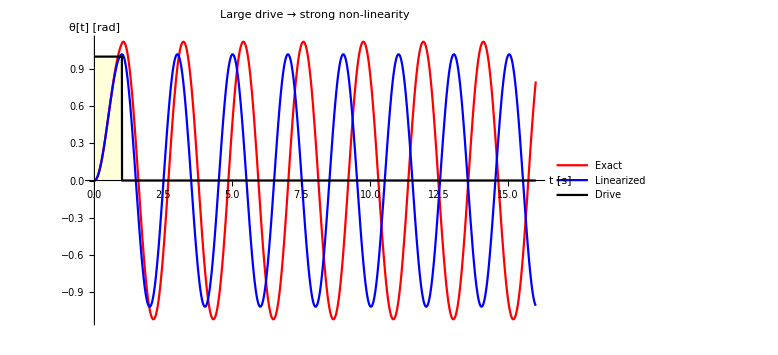

```mathematica
Plot[{θ[t]/.dsol,θ[t]/.dsoll,tdrive[t,1,1]},{t,0,16}, 
PlotStyle->{Red,Blue,{Black,Thin}},
Filling->{1-> None,2-> None,3->Axis},
FillingStyle->{White,White,LightYellow}, 
PlotLegends->{"Exact","Linearized","Drive"},
AxesLabel->{"t [s]","θ[t] [rad]"},
Exclusions->None, 
BaseStyle->{FontSize->18},
ImageSize->Large,
PlotLabel->"Large drive → strong non-linearity"]
```

Solve the differential equations again, with a weak drive:

```mathematica
dsol2=NDSolve[{deqn/.param2,θ[0]==0,θ'[0]==0},θ[t],{t,0,16}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

```mathematica
dsol2l=NDSolve[{deqnl/.param2,θ[0]==0,θ'[0]==0},θ[t],{t,0,16}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

Plot the results:

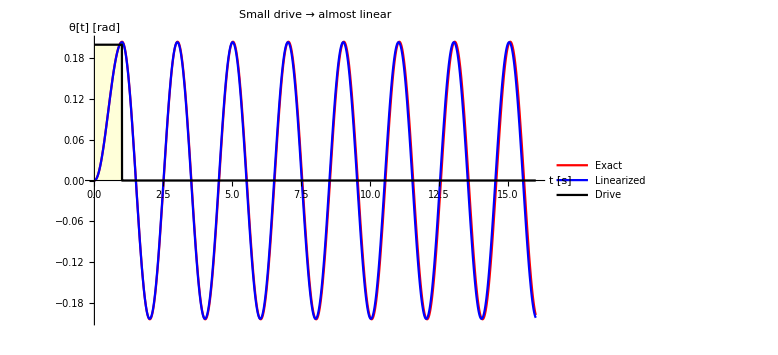

```mathematica
Plot[{θ[t]/.dsol2,θ[t]/.dsol2l,tdrive[t,0.2,1]},{t,0,16}, 
PlotStyle->{Red,Blue,{Black,Thin}},
Filling->{1-> None,2-> None,3->Axis},
FillingStyle->{White,White,LightYellow}, 
PlotLegends->{"Exact","Linearized","Drive"},
AxesLabel->{"t [s]","θ[t] [rad]"},
Exclusions->None,
BaseStyle->{FontSize->18},
ImageSize->Large,
PlotLabel->"Small drive → almost linear"]
```

#### Conclusions:

For a small drive, the linearization is a good option to be used. For a strong drive, the difference between the calculations with the linearized model significantly differ from the calculations with the non-linear model.